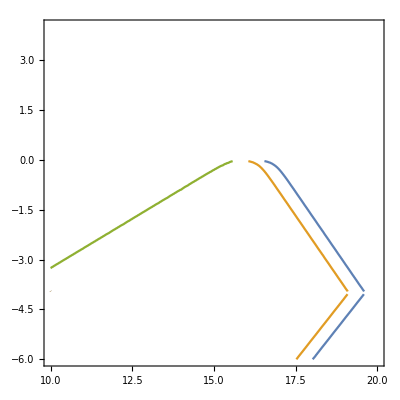

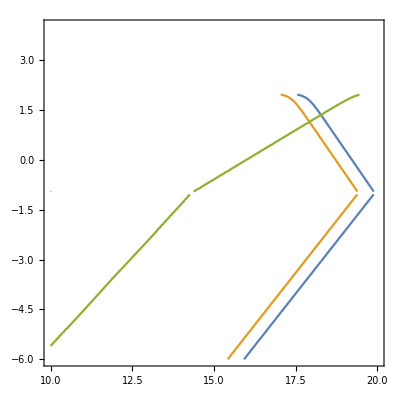

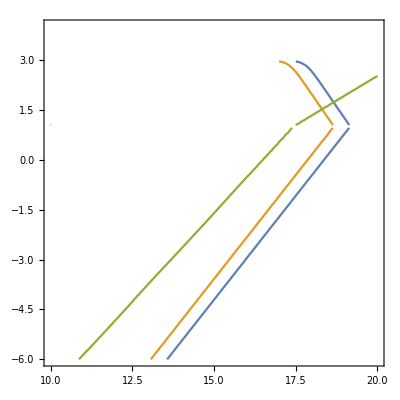

```mathematica
(* Tbh in TeV and distance in cm, Flux in cm^-2 sec^-1 *)
Flux[dist_,Tbh_]:=1.4 10^29 Tbh^1.6/(4 Pi dist^2);

(* time to evaporation ie remaining lifetime in sec *)
TauEvap[Tbh_]:=407(1.06/Tbh)^3;

(* The first condition is to have at least X photons during the explosion; assuming that we start the observation a given time t0 to evaporation, we have that the longest observation time is that time t0*)

(* Note that a detector with a low and high energy threshold will only be sensitive to BH evaporation within that time-frame, corresponding to TauEvap of that threshold... *)

EffectiveTime[Tbh_,ELow_,EHigh_]:=If[Tbh>EHigh,10^-99,If[Tbh<ELow,TauEvap[ELow]-TauEvap[EHigh],TauEvap[Tbh]-TauEvap[EHigh]]];

(* Now let's see when a given detector can see 10 photons *)
(* let's use log10 scale for both Tbh and distance in cm *)

Aeff=0.8 10^4;

(*ContourPlot[Aeff*EffectiveTime[10^logtempBH,10^-4,1.]*Flux[10^logdis,10^logtempBH]==10.,{logdis,10,20},{logtempBH,-6,2}]*)

(* Now let's assume the background is: note energy in GeV here ...*)

GammaBack[ene_]:=1.4 10^(-6) ene^(-2.1);

(* Now let's assume that the average photon energy is... *)
AveragePhotonEnergy[Tbh_]:=10. Tbh^0.5;

(* and we want S/B=5 *)

(* Angular resolution of the LAT *)
deltaOmega=10^-3;
Aeff=0.8 10^4;
EL=0.1 10^-3;
EH=1.;

ContourPlot[{Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==10.,Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==100.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==5.},{logdis,10,20},{logtempBH,-6,4}]

(* Now for HAWC *)
deltaOmega=10^-5;
Aeff=5 10^4 10^4;
EL=0.1 ;
EH=10^2;

ContourPlot[{Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==10.,Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==100.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==5.},{logdis,10,20},{logtempBH,-6,4}]

(* Now for LHAASO *)
deltaOmega=10^-4;
Aeff=10^6 10^4;
EL=10. ;
EH=10^3;

ContourPlot[{Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==10.,Aeff*EffectiveTime[10^logtempBH,EL,EH]*Flux[10^logdis,10^logtempBH]==100.,Flux[10^logdis,10^logtempBH]/Sqrt[EffectiveTime[10^logtempBH,EL,EH]*deltaOmega*AveragePhotonEnergy[10^logtempBH]*GammaBack[AveragePhotonEnergy[10^logtempBH]]]==5.},{logdis,10,20},{logtempBH,-6,4}]
```